```mathematica
xp = xs*Series[-Sqrt[(xt-xs)^2+y^2],{y,c,3}]
```

-xs √(c^2+xs^2-2 xs xt+xt^2)-(c xs (y-c))/(√(c^2+xs^2-2 xs xt+xt^2))-((xs (xs^2-2 xs xt+xt^2)) (y-c)^2)/(2 (c^2+xs^2-2 xs xt+xt^2)^(3/2))+(xs (c xs^2-2 c xs xt+c xt^2) (y-c)^3)/(2 (c^2+xs^2-2 xs xt+xt^2)^(5/2))+O[y-c]^4

```mathematica
xps = ReplaceAll[Normal[xp], y->0]
```

-(c^2 xs (xs^2-2 xs xt+xt^2))/(2 (c^2+xs^2-2 xs xt+xt^2)^(3/2))+(c^2 xs)/(√(c^2+xs^2-2 xs xt+xt^2))-xs √(c^2+xs^2-2 xs xt+xt^2)-(c^3 xs (c xs^2-2 c xs xt+c xt^2))/(2 (c^2+xs^2-2 xs xt+xt^2)^(5/2))

```mathematica
(*Plot[xp2/.xt->.4,{xs,0.35,0.45}]*)
```

```mathematica
qbx =Assuming[{xt>-1,xt<1,c>0},Integrate[xps,{xs,-1,1}]]
```

-((c^2 (3 √(c^2+xt^2)-8 xt √(c^2+xt^2)+6 xt^2 √(c^2+xt^2)+xt^4 (√(c^2+(-1+xt)^2)-√(c^2+xt^2)))-(-1+xt)^2 (-2 √(c^2+xt^2)+5 xt √(c^2+xt^2)-3 xt^2 √(c^2+xt^2)-xt^3 √(c^2+xt^2)+xt^4 (-√(c^2+(-1+xt)^2)+√(c^2+xt^2))))/((c^2+(-1+xt)^2)^(3/2))+(c^2 (-3 √(c^2+xt^2)-8 xt √(c^2+xt^2)-6 xt^2 √(c^2+xt^2)+xt^4 (√(c^2+xt^2)-√(c^2+(1+xt)^2)))+(1+xt)^2 (-2 √(c^2+xt^2)-5 xt √(c^2+xt^2)-3 xt^2 √(c^2+xt^2)+xt^3 √(c^2+xt^2)+xt^4 (√(c^2+xt^2)-√(c^2+(1+xt)^2))))/((c^2+(1+xt)^2)^(3/2)))/(6 √(c^2+xt^2))

```mathematica
(*Plot[qbx,{xt,-1,1}]*)
```

```mathematica
qbxD=Assuming[{xt>-1,xt<1,c>0},Simplify[D[qbx,{xt,2}]]]
```

1/(2 ((c^2+(-1+xt)^2) (c^2+(1+xt)^2))^(7/2))(-4 c^12 (-1+xt^2) (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-2 xt (-1+xt^2)^6 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2)+xt (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2)))-c^2 xt (-1+xt^2)^4 (11 xt (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+13 xt^3 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+13 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+11 xt^2 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2)))-c^10 (30 xt^2 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+21 xt^4 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+11 (-√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+36 xt (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+4 xt^3 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2)))-c^8 (-9 √(c^2+(-1+xt)^2)+9 √(c^2+(1+xt)^2)-4 xt^2 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+79 xt^4 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+46 xt^6 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+85 xt (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+10 xt^3 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+17 xt^5 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2)))-c^4 (-1+xt^2)^2 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2)+26 xt^2 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+33 xt^4 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+36 xt^6 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+33 xt (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+38 xt^3 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+25 xt^5 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2)))-c^6 (-√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2)-15 xt^2 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+55 xt^4 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+35 xt^6 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+54 xt^8 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+71 xt (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+47 xt^3 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))-19 xt^5 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+29 xt^7 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))))

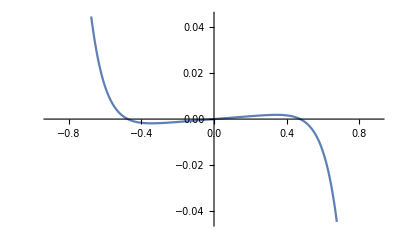

```mathematica
Plot[{qbxD/.c->1/4}+2xt,{xt,-0.9,0.9}]
```